## unemployment rate

### data

import data (FRED)

```mathematica
data={1900+FromDate[Normal[#[[1]]]]/(365.24*3600*24)+1/12.0,#[[2]]}&/@Drop[Import["C:\\Users\\dp864c\\Desktop\\SAVED DESKTOP\\UNRATE.xls"][[1]],11];
data=Cases[data,x_/;x[[1]]>1971.0];
```

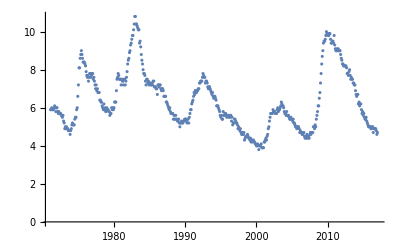

```mathematica
ListPlot[data]
```

here is the version voxeu.org plots (log V/U)

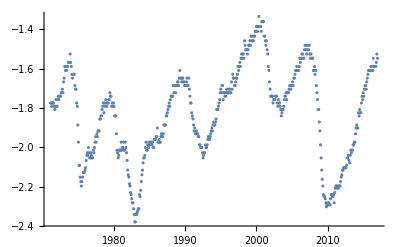

```mathematica
ListPlot[{#[[1]],Log[1/#[[2]]]}&/@data]
```

### entropy minimization

perform an entropy minimization over slope (α) values

```mathematica
binsize=0.025;
```

```mathematica
shannonfunction[p_]:=Module[{},If[p==0,0,-p Log[p]]];
listentropy[list_]:=Module[{},Total[shannonfunction/@list]/Log[Length[list]]];
```

```mathematica
entropydata=Table[
temp=Log[1/#[[2]]]-α*(#[[1]]-data[[1,1]])&/@data;
{α,listentropy[HistogramList[temp,{binsize},"Probability"][[2]]]}
,{α,0.00,0.5,0.001}];
```

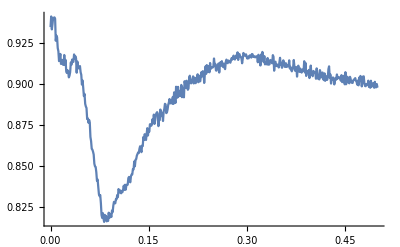

```mathematica
ListPlot[entropydata,Joined->True]
```

```mathematica
α0=(entropydata[[Position[entropydata,Min[entropydata[[All,2]]]][[1,1]]]])[[1]]
```

0.082

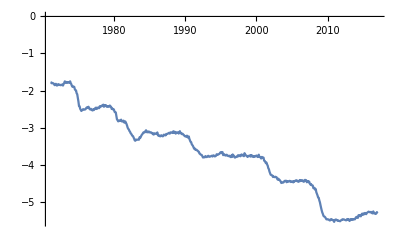

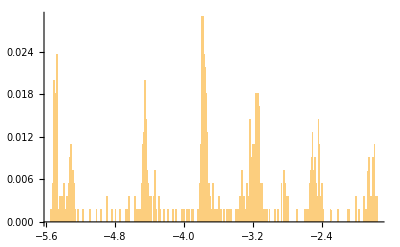

```mathematica
minent=(Log[1/#[[2]]]-α0*(#[[1]]-data[[1,1]]))&/@data;
ListPlot[Transpose[{data[[All,1]],minent}],Joined->True]
Histogram[minent,{0.01},"Probability"]
```

above is the entropy minimum histogram

### fit to function

next, fit min entropy data to sum of logistic functions

```mathematica
fitdata=Transpose[{data[[All,1]],minent}];
```

```mathematica
nlm=NonlinearModelFit[fitdata,a02/(1+Exp[-(y-y02)/b02])+a01/(1+Exp[-(y-y01)/b01])+a0/(1+Exp[-(y-y0)/b0])+a1/(1+Exp[-(y-y1)/b1])+a2/(1+Exp[-(y-y2)/b2])+a3/(1+Exp[(y-y3)/b3])+c,{{a02,1.0},{a01,1.0},{a0,1.0},{a1,2},{a2,3},{a3,0.1},{b02,0.2},{b01,0.2},{b0,0.2},{b1,0.2},{b2,0.2},{b3,0.2},{c,0},{y02,1974.8},{y01,1981.1},{y0,1991.1},{y1,2001.7},{y2,2008.8},{y3,2014.3}},y,Method->Automatic]
```

FittedModel[-2.53583+0.211818/(1+ⅇ^(-«19» (-«17»+y)))-(«18»)/(1+ⅇ^(«1»))-(«18»)/(1«1»«1»)-(«19»)/(1+«1»)+0.714338/(1+ⅇ^(«19»«1»(«1»«1»))-0.646548/(1+ⅇ^(-6.1399 (-«19»+y)))]

pretty decent fit (in entropy minimum space)

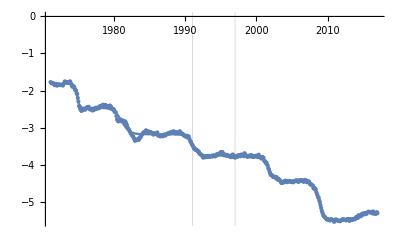

```mathematica
Show[ListPlot[Transpose[{data[[All,1]],minent}]],Plot[Normal[nlm],{y,data[[1,1]],data[[-1,1]]}],GridLines->{{1991,1997},{}}]
```

show the fit in log V/U space

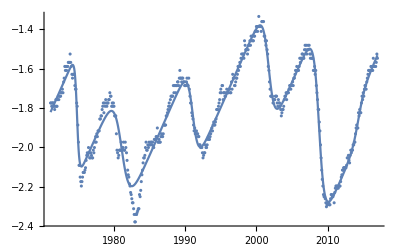

```mathematica
Show[ListPlot[{#[[1]],Log[1/#[[2]]]}&/@data],Plot[Normal[nlm]+α0*(y-data[[1,1]]),{y,data[[1,1]],data[[-1,1]]}]]
```

here is just V/U space ...

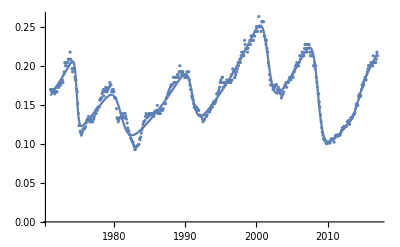

```mathematica
Show[ListPlot[{#[[1]],1/#[[2]]}&/@data],Plot[Exp[Normal[nlm]+α0*(y-data[[1,1]])],{y,data[[1,1]],data[[-1,1]]}]]
```

### show final graph

invert and show U/V on graph with the valued of the transitions ...

```mathematica
transitions={y02,y01,y0,y1,y2,y3}/.nlm["BestFitParameters"]
```

{1974.8,1981.07,1991.05,2001.72,2008.79,2014.33}

```mathematica
bands90=nlm["SinglePredictionBands"];
perr=Plot[Evaluate[1/Exp[bands90+α0*(y-data[[1,1]])]],{y,data[[1,1]],2018},PlotStyle->None,Filling->{1->{2}},FillingStyle->Directive[Lighter[Red],Opacity[0.2]]];
```

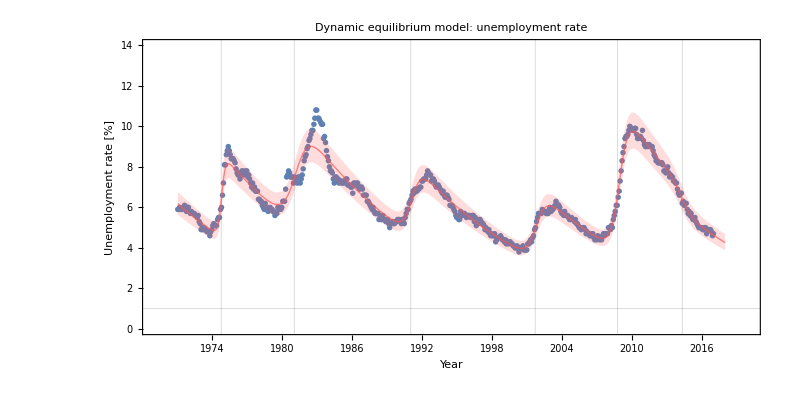

```mathematica
Show[ListPlot[{#[[1]],#[[2]]}&/@data,PlotStyle->PointSize[0.005]],perr,Plot[1/Exp[Normal[nlm]+α0*(y-data[[1,1]])],{y,data[[1,1]],2018},PlotStyle->Directive[Thick,Lighter[Red],Opacity[0.7]]],PlotRange->{{data[[1,1]]-2,2020},{0,14}},AspectRatio->1/2,ImageSize->11*72,BaseStyle->{FontSize->15},Frame->{True,True,False,False},FrameLabel->{"Year\n","\nUnemployment rate [%]"},GridLines->{transitions,{1}},Axes->False,PlotLabel->"\nDynamic equilibrium model: unemployment rate"]
```

```mathematica
U=Interpolation[data,InterpolationOrder->1];
```

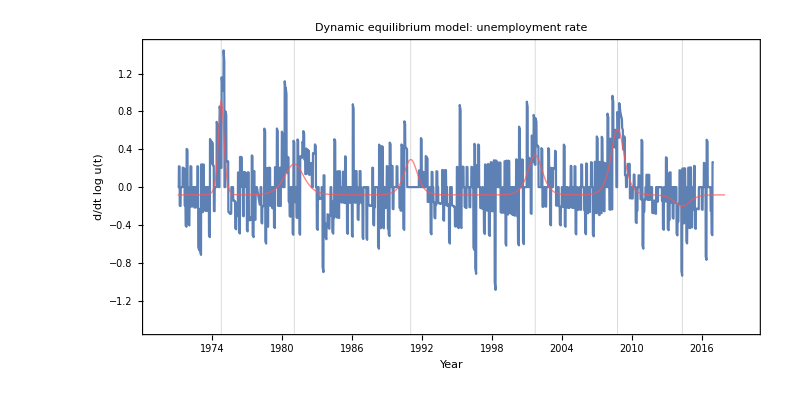

```mathematica
Show[Plot[D[Log[U[y]],y]/.y->yy,{yy,data[[1,1]],data[[-1,1]]}],Plot[D[Log[1/Exp[Normal[nlm]+α0*(y-data[[1,1]])]],y]/.y->yy,{yy,data[[1,1]],2018},PlotStyle->Directive[Thick,Lighter[Red],Opacity[0.7]],PlotRange->All],PlotRange->{{data[[1,1]]-2,2020},{-1.5,1.5}},AspectRatio->1/2,ImageSize->11*72,BaseStyle->{FontSize->15},Frame->{True,True,False,False},FrameLabel->{"Year\n","\nd/dt log u(t)"},GridLines->{transitions,{}},Axes->False,PlotLabel->"\nDynamic equilibrium model: unemployment rate"]
```

## latest data

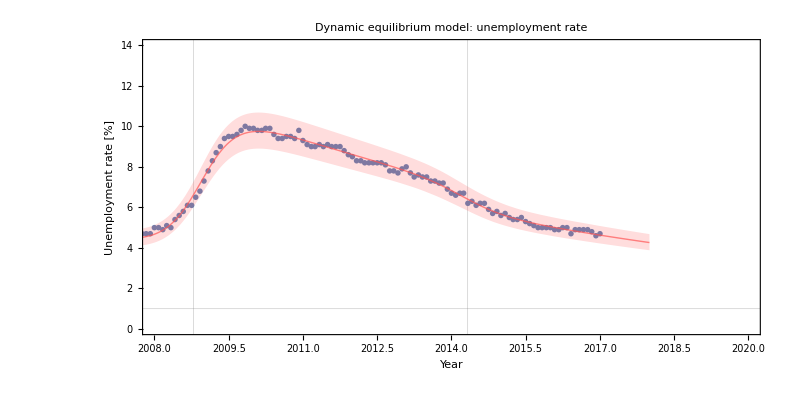

```mathematica
Show[ListPlot[{#[[1]],#[[2]]}&/@data,PlotStyle->PointSize[0.005]],perr,Plot[1/Exp[Normal[nlm]+α0*(y-data[[1,1]])],{y,data[[1,1]],2018},PlotStyle->Directive[Thick,Lighter[Red],Opacity[0.7]]],PlotRange->{{2008,2020},{0,14}},AspectRatio->1/2,ImageSize->11*72,BaseStyle->{FontSize->15},Frame->{True,True,False,False},FrameLabel->{"Year\n","\nUnemployment rate [%]"},GridLines->{transitions,{1}},Axes->False,PlotLabel->"\nDynamic equilibrium model: unemployment rate"]
```

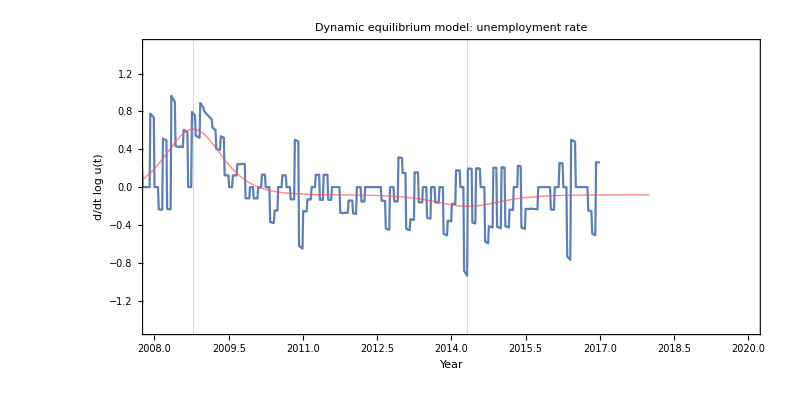

```mathematica
Show[Plot[D[Log[U[y]],y]/.y->yy,{yy,data[[1,1]],data[[-1,1]]}],Plot[D[Log[1/Exp[Normal[nlm]+α0*(y-data[[1,1]])]],y]/.y->yy,{yy,data[[1,1]],2018},PlotStyle->Directive[Thick,Lighter[Red],Opacity[0.7]],PlotRange->All],PlotRange->{{2008,2020},{-1.5,1.5}},AspectRatio->1/2,ImageSize->11*72,BaseStyle->{FontSize->15},Frame->{True,True,False,False},FrameLabel->{"Year\n","\nd/dt log u(t)"},GridLines->{transitions,{}},Axes->False,PlotLabel->"\nDynamic equilibrium model: unemployment rate"]
```